EUR/CHF = 0.834373

EUR/USD = 3.87944

USD/CAD = 28.9074

Profit = 44361.7

when = 45.084

{0.213128,1.9751}

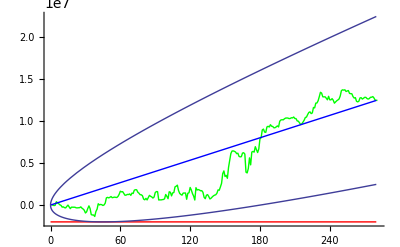

```mathematica
Clear[α,Σ];
p=0.95;
loss= 2000000;
y=y/.FindRoot[1+Erf[y/(√2)]==2p,{y,0}];
symbols = {"EUR/CHF", "EUR/USD","USD/CAD"};

equity={
{10000000,10000000,10000000,10000000,10000000,10000000,10000000,10000000,10000000,9999250,9999450,9994150,9995250,9994550,9994450,9997050,9996700,9995600,9994600,9994050,9994400,9992150,9988450,9991900,9993300,9990700,9992200,9992050,9988400,9989850,9990500,9990800,9993450,9990300,9983950,9987350,9987750,9987750,9987800,9987800,9987750,9987200,9987700,9987750,9987850,9987750,9987750,9987750,9987800,9987800,9987850,9987800,9987800,9987600,9987850,9987800,9987800,9987850,9987800,9987850,9987750,9987750,9987750,9985310,9967410,9957810,9956910,9958310,9936310,9946410,9940810,9945110,9949810,9953910,9950710,9935310,9973570,9973570,9973770,9973170,9972570,9974070,9976170,9985670,9997070,9988570,9979070,9980170,9976170,9974470,9975570,9976370,9978570,9974370,9973670,9978670,9978570,9979770,9974470,9975970,9977170,9973270,9975870,9973770,9973570,9974170,9918170,9929570,9954020,9937970,9905570,9900770,9894170,9894770,9893270,9898820,9893270,9973370,10010130,10018730,10009430,9991830,9983630,9943330,9983530,9975130,9975430,9963430,9950680,9952330,9926980,9881380,9874480,9867130,9841830,9830830,9870030,9894230,9910230,9906630,9915290,9902540,9842540,9831140,9824740,9808140,9775390,9781640,9775140,9734640,9734390,9658890,9564040,9562240,9603790,9644040,9647190,9636340,9669440,9593890,9637190,9668290,9643440,9669440,9706240,9710610,9742060,9779770,9762870,9798170,9773220,9727070,9742670,9777620,9776870,9780820,9812630,9813530,9813240,9810840,9819140,9832140,9844540,9853750,9853950,9849350,9853950,9853750,9854350,9855660,9829560,9814760,9818860,9806530,9867630,9824180,9748480,9703480,9703780,9714630,9636930,9660640,9629440,9715440,9713840,9608640,9519040,9627040,9611040,9702240,9709040,9573440,9488240,9519840,9520290,9581090,9610890,9586390,9573140,9634890,9783950,9720850,9726350,9690550,9757950,9748250,9688350,9765400,9765350,9754550,9761100,9790350,9828950,9844900,9854800,9766250,9830600,9842900,9892830,9889590,9897540,9889940,9891300,9907950,9913950,9911850,9907050,9913350,9886650,9926400,9937410,9947860,9955870,9946650,9954510,9955480,9963660,9958800,9963410,9970420,9975490,9976580,10014020,9996790,10002230,9991600,9984550,10003420,9982470,10035030,10024720,10011960,10041300,10034260,10069610,10065970,10074270,10053500,10044600,10037920,10055410},
{10000000,10000000,10000000,10000000,10003650,10001000,10001150,10012000,10005950,10009700,10001250,10009700,10015950,10017960,10017960,10023160,10025460,10035920,10035920,10035920,10033970,10017220,10015770,10021420,10021470,10021420,10021420,10021270,10018880,9998780,10001280,10010580,10021180,10005780,9974480,9964280,9954080,9957680,10000440,9993740,9984790,9966640,9967240,9960340,9935890,9941290,9939490,9967690,9970240,9946840,9964390,9988690,9952990,9965890,9969640,9964240,9960340,9971590,9983890,10006990,10010590,9980740,10008790,9999640,9961990,9934240,9932440,9948790,9919090,9877790,9868590,9909790,9923990,9943500,9926850,9953050,9965250,9947850,9946500,9941150,9924050,9913110,9931510,9979910,10029820,10008520,10016920,10029520,10002220,9982870,9975370,9978370,9968120,9961370,9906030,9970030,9961830,9974630,9888630,9895630,9917030,9933830,9941830,9895230,9804130,9723630,9638780,9696680,9768090,9702090,9647640,9651540,9583140,9477040,9477740,9494540,9327940,9496290,9605900,9621600,9592000,9499860,9495310,9390660,9519810,9452610,9464860,9452260,9431560,9435160,9391010,9249470,9220270,9214270,9243070,9267870,9381070,9364670,9439870,9446530,9519680,9507780,9563780,9569380,9589330,9523530,9484680,9513030,9533680,9555380,9568680,9499380,9427980,9458430,9656880,9692740,9681640,9658540,9727240,9728740,9767440,9737440,9736840,9715540,9785740,9794440,9900600,9905600,9885600,9910850,9893850,9821100,9892700,9890950,9897050,9920850,9923250,9927650,9954700,9951900,9956500,10018820,10028420,10015220,10020320,10040020,10041120,10027420,10018820,9939540,9936890,9901040,9902540,9929690,9946740,9923640,9933840,9924320,9917120,9876320,9879320,9900920,9920420,9954920,9949220,9896120,9901820,9974420,9986420,10032780,10028780,9994030,9931280,9952280,9922580,9923180,9971780,10034490,10100490,10108240,10135990,10126490,10124490,10133990,10235550,10279550,10239950,10316950,10313950,10294150,10345410,10361160,10362960,10410660,10406460,10368210,10428020,10440420,10442220,10445020,10456420,10430320,10441320,10453820,10462220,10470530,10465730,10468030,10415130,10455630,10449230,10453430,10454130,10445460,10430270,10419920,10438220,10437240,10441240,10434730,10447100,10462520,10431960,10485590,10477910,10515570,10515690,10518100,10527960,10547400,10548240,10513560,10489890,10507410,10538700,10543170,10564050,10521540,10457340,10454760,10447480},
{10000000,10000000,9997800,9999100,10013110,10009260,10005510,9999410,9997810,9990210,9992510,9988110,9986310,9992210,9997610,9989310,9981960,9986710,9986510,9986460,9986610,9986510,9986610,9986260,9986610,9989960,9984570,9981070,9976470,9967870,9972170,9984570,9993970,9985070,9964470,9964370,9965670,9959170,9973870,9984270,10007830,10005380,10007280,10007180,10007130,10008680,10016100,10034300,10035900,10036860,10036860,10036860,10036810,10036310,10036960,10036810,10036710,10039760,10046910,10056190,10053090,10057890,10046690,10040690,10046990,10053690,10053490,10053690,10052590,10067090,10066790,10074750,10074600,10071750,10064150,10056850,10048050,10049950,10046250,10033050,10032550,10039950,10030850,10033550,10035850,10035050,10031750,10025350,10033350,10054350,10059350,10058550,10025650,10027350,10034450,10026850,10028550,10029650,10058950,10050550,10037950,10064250,10061050,10052350,10077150,10089160,10125530,10120130,10114180,10101680,10097880,10093080,10099580,10122440,10122440,10120240,10116940,10116940,10102850,10122450,10116350,10114350,10105050,10104050,10136260,10136010,10136210,10136260,10136260,10136310,10136260,10136010,10134320,10149880,10148830,10137980,10111780,10116430,10111130,10114730,10107530,10111130,10111530,10124980,10120980,10143780,10164780,10200590,10209290,10184540,10187540,10186940,10244390,10268920,10268920,10273420,10275270,10277070,10264070,10259220,10254620,10244720,10243520,10246320,10250670,10250770,10230220,10153820,10154170,10167770,10214620,10196870,10239620,10241270,10237620,10256670,10242970,10230770,10241820,10283370,10288020,10310850,10312650,10301750,10300050,10319850,10322250,10321050,10331660,10336110,10336060,10335810,10336060,10336060,10336110,10336060,10360330,10368130,10370180,10374730,10380780,10380180,10378880,10371580,10370080,10380780,10385530,10372130,10374630,10359430,10359630,10358630,10368480,10357980,10354580,10355780,10355780,10355780,10358440,10357440,10359640,10371340,10373940,10366540,10353640,10370600,10375750,10382820,10383820,10396120,10405630,10420690,10415990,10393990,10393890,10401890,10386190,10377590,10390390,10375790,10373590,10382490,10374390,10360190,10363940,10367690,10371740,10375290,10395400,10410920,10414820,10412670,10413640,10408170,10412010,10415150,10400680,10400020,10398800,10387840,10380080,10379700,10367830,10358610,10362160,10371040,10372140,10365640,10368160,10367920,10368040,10368190,10368250,10368310,10368310,10368100,10367650,10368280,10368160,10368310,10368040}
};
n = Dimensions[equity][[1]];
count = Length[equity[[1]]] -1;
equity = Table[Differences[equity[[i]]], {i, n}];
matrix=Table[N[Covariance[equity[[i]],equity[[j]] ] ],{i,n},{j,n}];
factor=√Max[matrix];


loss = loss/factor;


equity=Table[equity[[i]]/factor,{i,n}];
matrix=Table[N[Covariance[equity[[i]],equity[[j]] ] ],{i,n},{j,n}];
α=Sum[Subscript[x, i] N[Mean[equity[[i]]]],{i,n}];
Σ=Sum[y^2 Subscript[x, i] Subscript[x, j] matrix[[i,j]],{i,n},{j,n}];

system={α,Σ≤ 4 loss α};
solution = NMaximize[system,Table[{Subscript[x, i],0,1},{i,n}]];
Do[
Print[symbols[[i]], " = ", Subscript[x, i]/.solution[[2]]];
,{i, n}];
kTheBest= Table[Subscript[x, i]/.solution[[2]],{i, n}];
dataTheBest = {0};

Do[
deltaTheBest=Sum[kTheBest[[j]]equity[[j]][[i]], {j, n}];
dataTheBest = Append[dataTheBest, dataTheBest[[Length[dataTheBest]]] + deltaTheBest];
,{i, count}];

g0=ListPlot[dataTheBest  factor, Joined->True, PlotStyle->RGBColor[0,1,0]];
g1=Plot[-loss factor, {x, 0,count},PlotStyle->RGBColor[1,0,0]];
g2= Plot[factor solution[[1]] x, {x, 0,count}, PlotStyle->RGBColor[0, 0,1]];
g3 = Plot[factor (solution[[1]] x - y √(kTheBest. matrix .kTheBest x)),{x,0, count}];
g4 = Plot[factor (solution[[1]] x + y √(kTheBest. matrix .kTheBest x)),{x,0, count}];
Print["Profit = ", factor solution[[1]]];
Print["when = ", y^2(kTheBest. matrix .kTheBest)/(2 solution[[1]])^2];
q =Sum[equity[[i]] kTheBest[[i]], {i,n}];
MeanCI[q,ConfidenceLevel->0.9]
(* Green is the best *)
(* Red is custom *)
Show[g0, g1, g2, g3, g4]
```

```mathematica
Needs["PortfolioFunction`","d:\\Projects\\ForexTestServer\\trunk\\TestServer\\Mathematics\\Mathematica\\GUI\\PortfolioFunction.nb"]
```

Get::noopen: Cannot open "PortfolioFunction.nb".

Needs::nocont: Context "PortfolioFunction`" was not created when Needs was evaluated.

$Failed